# RMF plots

## Preliminaries

Set your working directory to the directory of this file

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bank/OneDrive - Universitaet Bern/Project_Claudia_AREES_2021/Plotting

Function to compute Hamming distance between two genotypes

```mathematica
hamDist[x_,y_]:=Total[Abs[x-y]]
```

## Figure 1 & S1: plot small RMF landscapes

Choose parameter combinations to be plotted

```mathematica
param={{0,0.2},{0.05,0.15},{0.1,0.1},{0.15,0.05},{0.2,0}};
L=3;
```

Prepare an empty table to be filled with the plots

```mathematica
graphTable=Table[0,{k,5},{l,5}];
```

### Plot and save landscapes as separate images

Create several replicates of plots for each parameter combination

RandomVariate::posprm: Parameter 0 at position 2 in NormalDistribution[0,0] is expected to be positive.

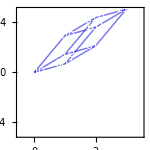

RandomVariate::posprm: Parameter 0 at position 2 in NormalDistribution[0,0] is expected to be positive.

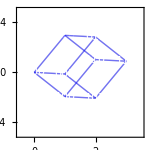

RandomVariate::posprm: Parameter 0 at position 2 in NormalDistribution[0,0] is expected to be positive.

General::stop: Further output of RandomVariate::posprm will be suppressed during this calculation.

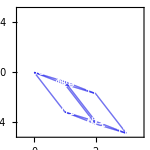

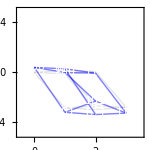

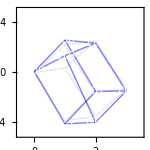

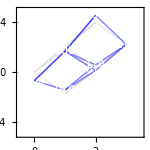

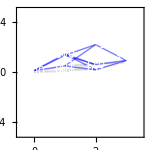

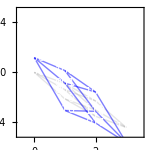

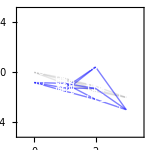

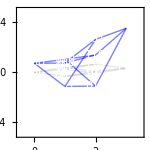

```mathematica
Do[
(* define variance of additive and epistatic effects *)
varAdd=param⟦k,2⟧;
varEpi=param⟦k,1⟧;
(* define genotypes as binary vectors *)
genotypes=Tuples[{0,1},L];
(* draw additive and epistatic effects from normal distributions; if variance is 0 create a table of 0s *)
effAdd=Check[RandomVariate[NormalDistribution[0,varAdd],L],Table[0,{L}]];
effEpi=Check[RandomVariate[NormalDistribution[0,varEpi],Length[genotypes]],Table[0,{Length[genotypes]}]];

(* compute the additive part of the fitness landscape *)
fitnessLandscapeAdd=Table[{genotypes⟦i⟧,Total[genotypes⟦i⟧],Sum[effAdd⟦j⟧genotypes⟦i,j⟧,{j,Length[genotypes⟦1⟧]}]},{i,Length[genotypes]}];
(* extract mutational paths from additive landscape *)
mutTableAdd=Select[Tuples[fitnessLandscapeAdd,2],Total[Abs[#⟦2,1⟧-#⟦1,1⟧]]==1&&Total[#⟦2,1⟧-#⟦1,1⟧]==1&];

(* compute RMF landscape with additive and epistatic parts *)
fitnessLandscape=Table[{genotypes⟦i⟧,Total[genotypes⟦i⟧],Sum[effAdd⟦j⟧genotypes⟦i,j⟧,{j,Length[genotypes⟦1⟧]}]+effEpi⟦i⟧},{i,Length[genotypes]}];
(* extract mutational paths *)
mutTable=Select[Tuples[fitnessLandscape,2],Total[Abs[#⟦2,1⟧-#⟦1,1⟧]]==1&&Total[#⟦2,1⟧-#⟦1,1⟧]==1&];

(* create plots of the landscapes *)
Print[xx=Graphics[{Gray,Opacity[0.2],
(* plot mutational paths of additive landscape *)
Table[Line[{mutTableAdd⟦k,1,{2,3}⟧,mutTableAdd⟦k,2,{2,3}⟧}],{k,Length[mutTable]}],
White, Opacity[1],
(* plot additive part of the landscape *)
Table[Style[Text[StringJoin[Map[ToString[#]&,fitnessLandscapeAdd⟦k,1⟧]],fitnessLandscapeAdd⟦k,{2,3}⟧], FontFamily-> "Andale Mono",Background->Directive[Opacity[0.2],Gray]],{k,Length[fitnessLandscape]}],
Blue,Opacity[0.5],
(* plot mutational paths of RMF landscape *)
Table[Line[{mutTable⟦k,1,{2,3}⟧,mutTable⟦k,2,{2,3}⟧}],{k,Length[mutTable]}],
White, Opacity[1],
(* plot genotypes of RMF landscape *)
Table[Style[Text[StringJoin[Map[ToString[#]&,fitnessLandscape⟦k,1⟧]],fitnessLandscape⟦k,{2,3}⟧], FontFamily-> "Andale Mono",Background->Directive[Opacity[0.5],Darker[Blue]]],{k,Length[fitnessLandscape]}]
},
PlotRange->{{-0.5,L+0.5},{-0.5,0.5}},
Frame->{True,True,False,False}, AspectRatio->1,FrameTicks->{{Automatic,None},{Table[k,{k,0,L}],None}},ImageSize->150,FrameStyle->Directive[12],ImagePadding->{{30, 10}, {30, 10}}]];
(* export each image *)
Export["RMFplot_"<> ToString[k]<>"_"<>ToString[i]<>".pdf",xx],
(* do this for all parameter combinations and a couple of replicates *)
{k,Length[param]},{i,3}]
```

### Plot grid

Same code as above, except that the graphs are being combined in a “GraphicsGrid”

RandomVariate::posprm: Parameter 0 at position 2 in NormalDistribution[0,0] is expected to be positive.

General::stop: Further output of RandomVariate::posprm will be suppressed during this calculation.

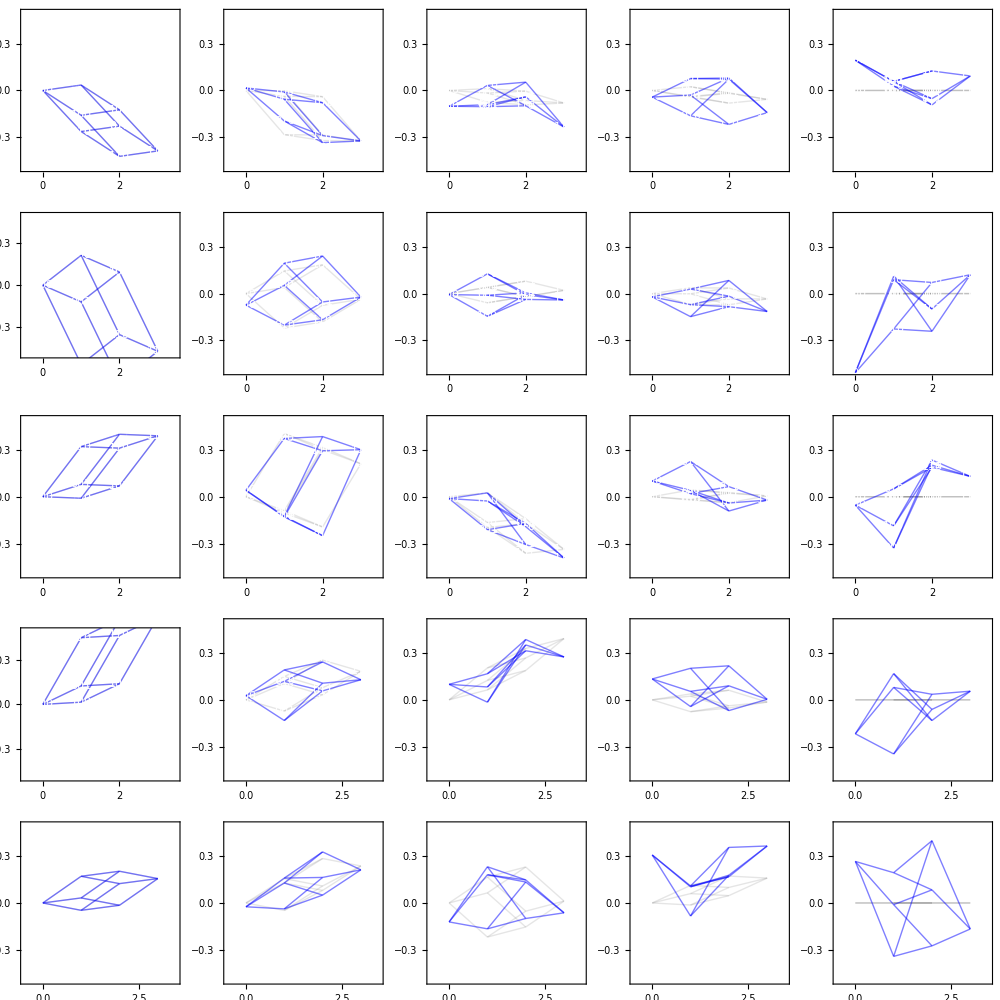

```mathematica
Do[
varAdd=param⟦k,2⟧;
varEpi=param⟦k,1⟧;
genotypes=Tuples[{0,1},L];

effAdd=Check[RandomVariate[NormalDistribution[0,varAdd],L],Table[0,{L}]];
effEpi=Check[RandomVariate[NormalDistribution[0,varEpi],Length[genotypes]],Table[0,{Length[genotypes]}]];

fitnessLandscapeAdd=Table[{genotypes⟦i⟧,Total[genotypes⟦i⟧],Sum[effAdd⟦j⟧genotypes⟦i,j⟧,{j,Length[genotypes⟦1⟧]}]},{i,Length[genotypes]}];
mutTableAdd=Select[Tuples[fitnessLandscapeAdd,2],Total[Abs[#⟦2,1⟧-#⟦1,1⟧]]==1&&Total[#⟦2,1⟧-#⟦1,1⟧]==1&];

fitnessLandscape=Table[{genotypes⟦i⟧,Total[genotypes⟦i⟧],Sum[effAdd⟦j⟧genotypes⟦i,j⟧,{j,Length[genotypes⟦1⟧]}]+effEpi⟦i⟧},{i,Length[genotypes]}];
mutTable=Select[Tuples[fitnessLandscape,2],Total[Abs[#⟦2,1⟧-#⟦1,1⟧]]==1&&Total[#⟦2,1⟧-#⟦1,1⟧]==1&];

graphTable⟦i,k⟧=Graphics[{Gray,Opacity[0.2],
Table[Line[{mutTableAdd⟦k,1,{2,3}⟧,mutTableAdd⟦k,2,{2,3}⟧}],{k,Length[mutTable]}],
White, Opacity[1],
Table[Style[Text[StringJoin[Map[ToString[#]&,fitnessLandscapeAdd⟦k,1⟧]],fitnessLandscapeAdd⟦k,{2,3}⟧], FontFamily-> "Andale Mono",Background->Directive[Opacity[0.2],Gray]],{k,Length[fitnessLandscape]}],
Blue,Opacity[0.5],
Table[Line[{mutTable⟦k,1,{2,3}⟧,mutTable⟦k,2,{2,3}⟧}],{k,Length[mutTable]}],
White, Opacity[1],
Table[Style[Text[StringJoin[Map[ToString[#]&,fitnessLandscape⟦k,1⟧]],fitnessLandscape⟦k,{2,3}⟧], FontFamily-> "Andale Mono",Background->Directive[Opacity[0.5],Darker[Blue]]],{k,Length[fitnessLandscape]}]
},
PlotRange->{{-0.5,L+0.5},{-0.5,0.5}},
Frame->{True,True,False,False}, AspectRatio->1,FrameTicks->{{Automatic,None},{Table[k,{k,0,L}],None}},ImageSize->150,FrameStyle->Directive[12],ImagePadding->{{30, 10}, {30, 10}}],
{k,Length[param]},{i,5}]
xx=GraphicsGrid[graphTable,ImageSize->1000]
```

Export the resulting graphics

```mathematica
Export["RMFgrid.pdf",xx]
```

RMFgrid.pdf

## Figure 1 & S2 - random adaptive walks on larger RMF landscape

RandomVariate::posprm: Parameter 0 at position 2 in NormalDistribution[0,0] is expected to be positive.

1

1

3409

7.32548

{0.,0.,Mean[{}],Median[{}]}

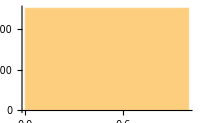

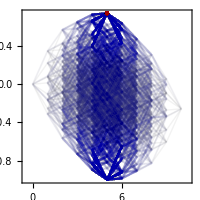

3

3

2887

7.1149

{1.66258,2.,2.85536,3}

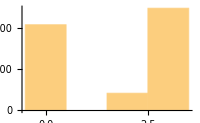

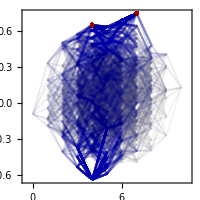

58

55

1239

6.28683

{4.39317,5.,4.60274,5}

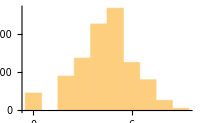

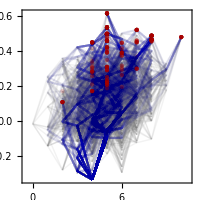

77

49

525

5.25786

{4.23982,4.,4.5523,5}

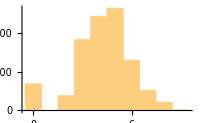

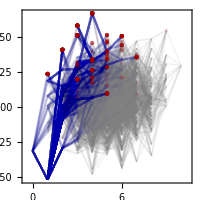

RandomVariate::posprm: Parameter 0 at position 2 in NormalDistribution[0,0] is expected to be positive.

98

57

354

4.86475

{3.69464,4.,3.99807,4}

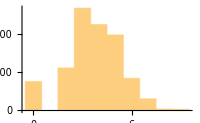

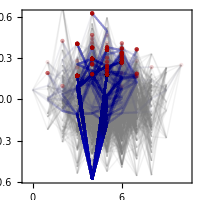

```mathematica
(* define parameter combinations to use, and size of landscape *)
param={{0,0.2},{0.05,0.15},{0.1,0.1},{0.15,0.05},{0.2,0}};
L=10;
Do[
(* define variance of additive and epistatic effects *)
varAdd=param⟦k,2⟧;
varEpi=param⟦k,1⟧;
(* define genotypes as binary vectors *)
genotypes=Tuples[{0,1},L];
(* draw additive and epistatic effects from normal distributions *)
effAdd=Check[RandomVariate[NormalDistribution[0,varAdd],L],Table[0,{L}]];
effEpi=Check[RandomVariate[NormalDistribution[0,varEpi],Length[genotypes]],Table[0,{Length[genotypes]}]];
(* compute RMF landscape *)
fitnessLandscape=Table[{genotypes⟦i⟧,Total[genotypes⟦i⟧],Sum[effAdd⟦j⟧genotypes⟦i,j⟧,{j,Length[genotypes⟦1⟧]}]+effEpi⟦i⟧},{i,Length[genotypes]}];
(* extract mutational paths *)
mutTable=Select[Tuples[fitnessLandscape,2],Total[Abs[#⟦2,1⟧-#⟦1,1⟧]]==1&&Total[#⟦2,1⟧-#⟦1,1⟧]==1&];
(* compute number of maxima in the landscape *)
Print[Count[Table[Length[Select[fitnessLandscape,#⟦3⟧>fitnessLandscape⟦k,3⟧&&hamDist[#⟦1⟧,fitnessLandscape⟦k,1⟧]==1&]],{k,Length[fitnessLandscape]}],0]];
(* identify least fit genotype as starting point for the simulations *)
leastFitGenotype=fitnessLandscape⟦Position[fitnessLandscape,Min[fitnessLandscape⟦All,3⟧]]⟦1,1⟧⟧;

(* create empty set of random walks *)
listOfRandomWalks={};
listOfPaths={};
Do[
(* set starting genotype *)
focal=leastFitGenotype;
(* select all better neighbors*)
goodNeighbors=Select[fitnessLandscape,#⟦3⟧>focal⟦3⟧&&hamDist[#⟦1⟧,focal⟦1⟧]==1&];
(* start walk *)
randomWalk={focal};
While[Length[goodNeighbors]>0,
(* find fittest neighbor *)
randomNeighbor=RandomChoice[goodNeighbors];
(* add data point to table *)
AppendTo[randomWalk,randomNeighbor];
AppendTo[listOfPaths,{focal⟦3⟧,randomNeighbor⟦3⟧}];
(* set new focal genotype *)
focal=randomNeighbor;
(* find new neighbors *)
goodNeighbors=Select[fitnessLandscape,#⟦3⟧>focal⟦3⟧&&hamDist[#⟦1⟧,focal⟦1⟧]==1&];
(* stop in case of infinite loop for some reason *)
If[Length[randomWalk]==20,Break[]]];
AppendTo[listOfRandomWalks,randomWalk],
(* compute 1000 random adaptive walks like this *)
{1000}];
(* compute and print number of peaks reached *)
Print[reachedPeaks=DeleteDuplicates[listOfRandomWalks⟦All,-1,-1⟧]//Length];
(* compute and print number of unique paths taken *)
Print[numberOfUniqueSteps=DeleteDuplicates[listOfPaths]//Length];
(* compute and print entropy of unique paths *)
Print[entropyOfPaths=Entropy[listOfPaths]//N];
(* compute and pring average Hamming distance between peaks, with and without paths that reached the same peak *)
peakDist=Flatten[Table[Table[hamDist[listOfRandomWalks⟦i,-1,1⟧,listOfRandomWalks⟦j,-1,1⟧],{i,j-1}],{j,2,Length[listOfRandomWalks]}]];
Print[{Mean[peakDist]//N,Mean[DeleteCases[peakDist,0]]//N}];
(* visualize distance between peaks *)
Print[Histogram[peakDist]];

(* create plot of the random walks *)
Print[xx=ListPlot[listOfRandomWalks⟦All,All,2;;3⟧,Joined->True,PlotStyle->Directive[Darker[Blue],Opacity[0.02]],Epilog->{Darker[Red],Opacity[0.1],PointSize[Large],Table[Point[listOfRandomWalks⟦i,-1,{2,3}⟧],{i,Length[listOfRandomWalks]}]},
(* in the backhground plot the complete fitness landscape *)
Prolog->{
Gray,Opacity[0.1],
Table[Line[{mutTable⟦k,1,{2,3}⟧,mutTable⟦k,2,{2,3}⟧}],{k,Length[mutTable]}]
},
PlotRange->{{-0.5,L+0.5},All},
Frame->{True,True,False,False}, AspectRatio->1,FrameTicks->{{Automatic,None},{Table[k,{k,0,L}],None}},ImageSize->200,FrameStyle->Directive[12],ImagePadding->{{30, 10}, {30, 10}}]];
(* export the images *)
Export["RMFplotwithevolution_"<> ToString[k]<>".pdf",xx],
{k,5}]
```

## Figure 3: plot Hall et al. fitness landscapes

Prepare import of data

```mathematica
allLandscapesFiles=FileNames["./Data_formatted/*.txt"]
```

{./Data_formatted/landscape_acetate.txt,./Data_formatted/landscape_beef.txt,./Data_formatted/landscape_casamino.txt,./Data_formatted/landscape_glucose.txt,./Data_formatted/landscape_milk.txt,./Data_formatted/landscape_NAG.txt,./Data_formatted/landscape_rhamnose.txt,./Data_formatted/landscape_trypsin.txt}

Prepare naming of landscapes by the environment

```mathematica
names={"Acetate","Beef extract","Casamino acids","Glucose","Milk protein hydrosylate", "N-acetylglucosamine","Rhamnose","Trypsin"};
```

Create empty tables

```mathematica
allLandscapes=Table[0,{8}];
allLandscapesRaw=Table[0,{8}];
```

Upload data and convert to landscape format used in the other plots

```mathematica
Do[allLandscapesRaw⟦i⟧=Import[allLandscapesFiles⟦i⟧,"Table"]⟦2;;⟧;
allLandscapes⟦i⟧=Table[{allLandscapesRaw⟦i,k,1;;5⟧,Total[allLandscapesRaw⟦i,k,1;;5⟧],allLandscapesRaw⟦i,k,6⟧},{k,Length[allLandscapesRaw⟦i⟧]}]
,{i,8}]
```

Check output

```mathematica
allLandscapes⟦1⟧
```

{{{0,0,0,0,0},0,0.973153},{{0,0,0,0,1},1,0.921354},{{0,0,0,1,0},1,1.0074},{{0,0,0,1,1},2,0.929853},{{0,0,1,0,0},1,1.12348},{{0,0,1,0,1},2,1.08601},{{0,0,1,1,0},2,1.17254},{{0,0,1,1,1},3,0.99442},{{0,1,0,0,0},1,1.3998},{{0,1,0,0,1},2,1.36373},{{0,1,0,1,0},2,1.1297},{{0,1,0,1,1},3,1.21559},{{0,1,1,0,0},2,1.24261},{{0,1,1,0,1},3,1.22016},{{0,1,1,1,0},3,1.17518},{{0,1,1,1,1},4,1.20666},{{1,0,0,0,0},1,1.10865},{{1,0,0,0,1},2,0.982671},{{1,0,0,1,0},2,1.04897},{{1,0,0,1,1},3,1.06982},{{1,0,1,0,0},2,1.19404},{{1,0,1,0,1},3,1.07751},{{1,0,1,1,0},3,1.16496},{{1,0,1,1,1},4,1.25343},{{1,1,0,0,0},2,1.18778},{{1,1,0,0,1},3,1.12307},{{1,1,0,1,0},3,1.20761},{{1,1,0,1,1},4,1.10177},{{1,1,1,0,0},3,1.26972},{{1,1,1,0,1},4,1.22174},{{1,1,1,1,0},4,1.2636},{{1,1,1,1,1},5,1.16993}}

Extract minimal and maximal fitness across landscapes to define the plot ranges

```mathematica
rangeOfFitness={Min[allLandscapes⟦All,All,-1⟧]-0.1,Max[allLandscapes⟦All,All,-1⟧]+0.1}
```

{0.496778,2.23846}

Plot landscapes and save the plots

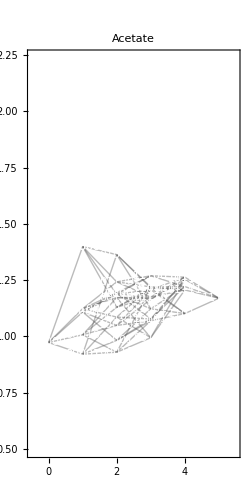

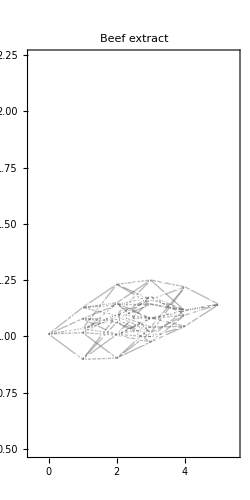

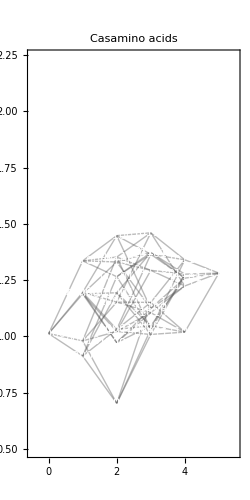

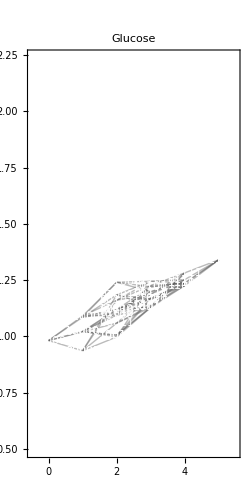

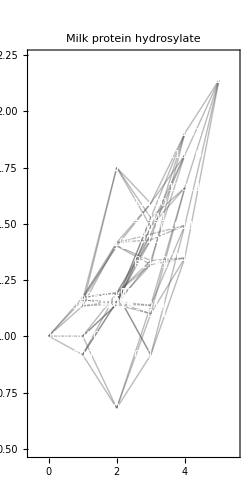

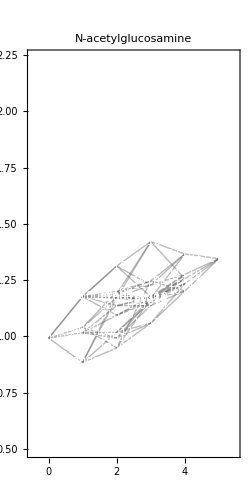

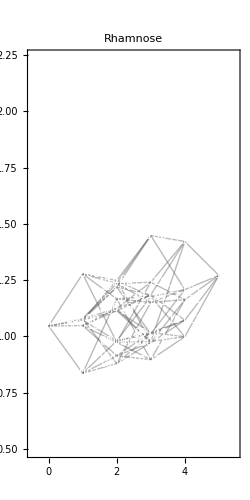

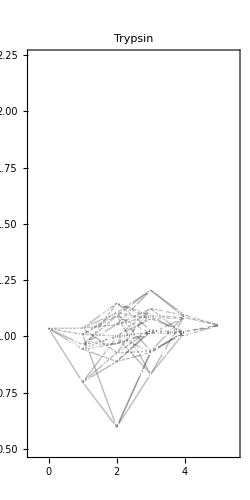

```mathematica
Do[
(* extract mutational paths *)
mutTable=Select[Tuples[allLandscapes⟦j⟧,2],Total[Abs[#⟦2,1⟧-#⟦1,1⟧]]==1&&Total[#⟦2,1⟧-#⟦1,1⟧]==1&];
(* identify peaks *)
peakIndices=Position[Table[Select[allLandscapes⟦j⟧,#⟦3⟧>allLandscapes⟦j⟧⟦k,3⟧&&hamDist[#⟦1⟧,allLandscapes⟦j⟧⟦k,1⟧]==1&],{k,Length[allLandscapes⟦j⟧]}],{}]//Flatten;
(* identify sinks *)
sinkIndices=Position[Table[Select[allLandscapes⟦j⟧,#⟦3⟧<allLandscapes⟦j⟧⟦k,3⟧&&hamDist[#⟦1⟧,allLandscapes⟦j⟧⟦k,1⟧]==1&],{k,Length[allLandscapes⟦j⟧]}],{}]//Flatten;
(* create graphics *)
Print[xx=Graphics[{
Darker[Gray],Opacity[0.4],
(* plot mutational paths *)
Table[Line[{mutTable⟦k,1,{2,3}⟧,mutTable⟦k,2,{2,3}⟧}],{k,Length[mutTable]}],
White, Opacity[1],
(* plot all genotypes, then peaks and valleys *)
Table[Style[Text[StringJoin[Map[ToString[#]&,allLandscapes⟦j⟧⟦k,1⟧]],allLandscapes⟦j⟧⟦k,{2,3}⟧], FontFamily-> "Andale Mono",Background->Directive[Opacity[0.5],Darker[Blue]]],{k,Length[allLandscapes⟦j⟧]}],
Table[Style[Text[StringJoin[Map[ToString[#]&,allLandscapes⟦j⟧⟦k,1⟧]],allLandscapes⟦j⟧⟦k,{2,3}⟧], FontFamily-> "Andale Mono",Background->Directive[Opacity[1],Darker[Red]]],{k,peakIndices}],
Table[Style[Text[StringJoin[Map[ToString[#]&,allLandscapes⟦j⟧⟦k,1⟧]],allLandscapes⟦j⟧⟦k,{2,3}⟧], FontFamily-> "Andale Mono",Background->Directive[Opacity[1],Black]],{k,sinkIndices}]
},
PlotRange->{{-0.5,5+0.5},rangeOfFitness},
(* name plots by the environment *)
PlotLabel->Style[names⟦j⟧,18],
Frame->{True,True,False,False}, AspectRatio->2,FrameTicks->{{Automatic,None},{Table[k,{k,0,5}],None}},ImageSize->250,FrameStyle->Directive[14],ImagePadding->{{30, 10}, {30, 10}}]];
(* export each image *)
Export["FL_"<> names⟦j⟧<>".pdf",xx],
{j,8}]
```

```mathematica
Select[allLandscapes⟦1⟧,#⟦3⟧>allLandscapes⟦1⟧⟦1,3⟧&&hamDist[#⟦1⟧,allLandscapes⟦1⟧⟦1,1⟧]==1&]
```

{{{0,0,0,1,0},1,1.0074},{{0,0,1,0,0},1,1.12348},{{0,1,0,0,0},1,1.3998},{{1,0,0,0,0},1,1.10865}}

```mathematica
peakIndices=Position[Table[Select[allLandscapes⟦1⟧,#⟦3⟧>allLandscapes⟦1⟧⟦k,3⟧&&hamDist[#⟦1⟧,allLandscapes⟦1⟧⟦k,1⟧]==1&],{k,Length[allLandscapes⟦1⟧]}],{}]//Flatten
sinkIndices=Position[Table[Select[allLandscapes⟦1⟧,#⟦3⟧<allLandscapes⟦1⟧⟦k,3⟧&&hamDist[#⟦1⟧,allLandscapes⟦1⟧⟦k,1⟧]==1&],{k,Length[allLandscapes⟦1⟧]}],{}]//Flatten
```

{9,24,29}

{2}